```mathematica
(* Logan Prust - Aer E 351 - Project R *)
```

```mathematica
Quit[] (* Clears all variables. *)
```

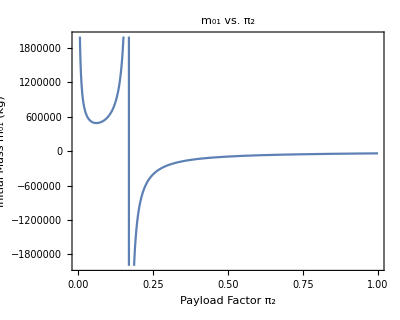

{491114.,{p2→0.0613791}}

```mathematica
p1[p2_]:=(Exp[(-Subscript[v, e2]Log[Subscript[ϵ, 2]+(1-Subscript[ϵ, 2])p2]-Subscript[v, T15]+Subscript[v, CK]-Subscript[v, drag])/Subscript[v, e1]]-Subscript[ϵ, 1])/(1-Subscript[ϵ, 1]) (* Subscript[π, 1] in terms of Subscript[π, 2]. "p" is used instead of π so that Mathematica did not confuse it with the irrational number π. *)
Subscript[m, 01][p2_]:=Subscript[m, 03]/(p2*p1[p2]) (* The initial mass as a function of Subscript[π, 1] and Subscript[π, 2]. *)
Subscript[m, 03]=4200; (* Payload mass of the second stage. *)
μ=398600;
Subscript[r, Earth]=6378;
Subscript[ω, Earth]=(2*Pi)/(24*3600); (* Angular velocity of the Earth. *)
Δi=28.5; (* Inclination of inital orbit in degrees. *)
Subscript[v, CK]=Subscript[ω, Earth] Subscript[r, Earth] Cos[Δi Degree]; (* Velocity of launch point (Cape Kennedy). *)
Subscript[r, Tp]=102+Subscript[r, Earth]; (* Radius of transfer orbit at perigee. *)
Subscript[r, Ta]=35786+Subscript[r, Earth]; (* Radius of transfer orbit at apogee. *)
Subscript[v, C3]=√(μ/Subscript[r, Ta]); (* Velocity of the circular geosynchronous orbit. *)
Subscript[v, Tp]=√((2μ)/Subscript[r, Tp]-(2μ)/(Subscript[r, Tp]+Subscript[r, Ta])); (* Velocity of the transfer orbit at perigee. *)
Subscript[v, Ta]=√((2μ)/Subscript[r, Ta]-(2μ)/(Subscript[r, Tp]+Subscript[r, Ta])); (* Velocity of the transfer orbit at apogee. *)
Subscript[Δv, 3]=√(Subscript[v, Ta]^2+Subscript[v, C3]^2-2 Subscript[v, Ta] Subscript[v, C3] Cos[Δi Degree]); (* The change in the velocity provided by the third stage. *)
Subscript[a, T]=(Subscript[r, Tp]+Subscript[r, Ta])/2; (* Semi-major axis of the transfer orbit. *)
Subscript[H, T]=Subscript[r, Ta] Subscript[v, Ta]; (* Angular momentum of the transfer orbit. *)
Subscript[p, T]=Subscript[H, T]^2/μ; (* Semi-latus parameter of the transfer orbit. *)
Subscript[e, T]=√(1-Subscript[p, T]/Subscript[a, T]); (* Eccentricity of the transfer orbit. *)
Subscript[r, T15]=Subscript[p, T]/(1+Subscript[e, T] Cos[15 Degree]); (* Radius of the transfer orbit at a true anomaly of 15°. *)
Subscript[v, T15]=√((2μ)/Subscript[r, T15]-μ/Subscript[a, T]); (* Velocity of the transfer orbit at a true anomaly of 15°. *)
Subscript[v, drag]=1.3; (* The additional change in velocity that must be provided by the second stage to correct for drag and other factors. *)
Subscript[I, sp1]=250; (* Specific impulses. *)
Subscript[I, sp2]=455;
Subscript[I, sp3]=240;
g=.00981; (* Gravitational acceleration. *)
Subscript[ϵ, 1]=.11; (* Structure factors. *)
Subscript[ϵ, 2]=.13;
Subscript[ϵ, 3]=.15;
Subscript[v, e1]=Subscript[I, sp1]*g; (* Exhaust velocities. *)
Subscript[v, e2]=Subscript[I, sp2]*g;
Subscript[v, e3]=Subscript[I, sp3]*g;
Plot[Subscript[m, 01][p2],{p2,0,1},PlotRange->{{0,1},{-2000000,2000000}},AspectRatio->.8,Frame->{True,True},FrameLabel->{"Payload Factor π_2","Initial Mass m_01 (kg)"},PlotLabel->"m_01 vs. π_2"] (* Plotting the initial mass as a function of the payload factor of the second stage. *)
FindMinimum[{Subscript[m, 01][p2],0≤p2≤.1},{p2,.01}] (* The most efficient rocket will have a mass that is at a minimum with respect to Subscript[π, 2]. *)
```

```mathematica
(* Negative masses are unphysical, so only the left portion of the graph need be considered. The minimum is clearly shown, and occurs at Subscript[π, 2]= 0.0613791 with a value of Subscript[m, 01]= 491114 kg. *)
```

```mathematica
Subscript[m, 01]=491114;
Subscript[p, 2]=0.0613791;
Subscript[p, 1]=p1[Subscript[p, 2]]; (* Now that Subscript[π, 2] is known, we need only to plug it into our equation for Subscript[π, 1]. *)
Subscript[p, 3]=(Exp[-Subscript[Δv, 3]/Subscript[v, e3]]-Subscript[ϵ, 3])/(1-Subscript[ϵ, 3]); (* Determination of Subscript[π, 3]. *)
Subscript[m, 02]=Subscript[p, 1] Subscript[m, 01]; (* Determination of initial mass of second stage. *)
```

```mathematica
A={{p,0,0,-1},{0,ϵ-1,ϵ,0},{1,-1,-1,-1},{-ϵ-(1-ϵ)p,1,0,1}};
B={{Subscript[m, 0]},{Subscript[m, s]},{Subscript[m, p]},{Subscript[m, star]}};
Solve[A.B==0,{Subscript[m, 0],Subscript[m, s],Subscript[m, p],Subscript[m, star]}] (* Determination of the eigenvector of the mass matrix. *)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{m_s→-(-ϵ+p ϵ) m_0,m_p→-(-1+p+ϵ-p ϵ) m_0,m_star→p m_0}}

```mathematica
M[m0_,ϵ_,p_]:={{-m0(-ϵ+ϵ p)},{-m0(-1+ϵ+p-ϵ p)},{m0 p}} (* The initial mass of each stage can be used to determine the masses of the components of the respective stages. *)
Solve[M[Subscript[m, 01],Subscript[ϵ, 1],Subscript[p, 1]]=={{Subscript[m, s1]},{Subscript[m, p1]},{Subscript[m, star1]}},{Subscript[m, s1],Subscript[m, p1],Subscript[m, star1]}]
Solve[M[Subscript[m, 02],Subscript[ϵ, 2],Subscript[p, 2]]=={{Subscript[m, s2]},{Subscript[m, p2]},{Subscript[m, star2]}},{Subscript[m, s2],Subscript[m, p2],Subscript[m, star2]}]
Solve[M[Subscript[m, 03],Subscript[ϵ, 3],Subscript[p, 3]]=={{Subscript[m, s3]},{Subscript[m, p3]},{Subscript[m, star3]}},{Subscript[m, s3],Subscript[m, p3],Subscript[m, star3]}]
```

{{m_s1→46495.6,m_p1→376191.,m_star1→68427.2}}

{{m_s2→8349.53,m_p2→55877.6,m_star2→4200.}}

{{m_s3→402.326,m_p3→2279.85,m_star3→1517.83}}

```mathematica
(* Velocities gained by the first two stages (Subscript[Δv, 3] has already been determined). *)
Subscript[Δv, 1]=-Subscript[v, e1]Log[Subscript[ϵ, 1]+(1-Subscript[ϵ, 1])Subscript[p, 1]];
Subscript[Δv, 2]=-Subscript[v, e2]Log[Subscript[ϵ, 2]+(1-Subscript[ϵ, 2])Subscript[p, 2]]+Subscript[v, drag];
```

```mathematica
(* First stage: *)
Subscript[m, 01]
Subscript[m, s1]=46495.6
Subscript[m, p1]=376191
Subscript[p, 1]
Subscript[Δv, 1]
```

491114

46495.6

376191

0.139331

3.56205

```mathematica
(* Second stage: *)
Subscript[m, 02]
Subscript[m, s2]=8349.53
Subscript[m, p2]=55877.6
Subscript[p, 2]
Subscript[Δv, 2]
```

68427.2

8349.53

55877.6

0.0613791

8.87057

```mathematica
(* Third stage: *)
Subscript[m, 03]
Subscript[m, s3]=402.326
Subscript[m, p3]=2279.85
Subscript[p, 3]
Subscript[Δv, 3]
```

4200

402.326

2279.85

0.361387

1.84274